```mathematica
Timing@(V[#]&/@Range[0.1,10,0.0001])
Timing@(Vs1[#,a,c1]&/@Range[0.1,10,0.0001])
```

{0.125,{-1.,-0.999001,-0.998004,-0.997009,-0.996016,-0.995025,-0.994036,-0.993049,-0.992063,-0.99108,-0.990099,-0.98912,98977,-0.0100011,-0.010001,-0.0100009,-0.0100008,-0.0100007,-0.0100006,-0.0100005,-0.0100004,-0.0100003,-0.0100002,-0.0100001,-0.01}}
 |  |  |  |

{1.53125,{(c1 ⅇ^(-0.005/a^2))/(2 √2 a π^(3/2))-1. Erf[0.0707107/a],(c1 ⅇ^(-0.00501001/a^2))/(2 √2 a π^(3/2))-0.999001 Erf[0.0707814/a],98997,(c1 ⅇ^(-49.999/a^2))/(2 √2 a π^(3/2))-0.0100001 Erf[7.071/a],(c1 ⅇ^(-50./a^2))/(2 √2 a π^(3/2))-0.01 Erf[7.07107/a]}}
 |  |  |  |

```mathematica
AbsoluteTiming@(V[#]&/@Range[0.1,10,0.0001])
```

## Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.01;u0=10^-20;δstart=10^-10;m=100;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- α/# Erf[#/(√2 a)]-2π α c2 a^2 δa[#]+(π α)/2 d1 a^4(-(3 ⅇ^(-#^2/(2 a^2)))/(2 √2 a^5 π^(3/2))+(ⅇ^(-#^2/(2 a^2)) #^2)/(2 √2 a^7 π^(3/2)))&[r];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
(*Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];*)
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[Table20REE],opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]]
δexpminus5=δ50e[10^-5,V[r]]
δ50V=δ50[V[r]]
```

NDSolve::precw: 微分方程的精度 ({{200 (1/10000000000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678812640161460360327585430028974190240877271907) 小于 WorkingPrecision (50.).

End with 0.6875011s

-0.00067881253589889958676131199718849591989776729252557

NDSolve::precw: 微分方程的精度 ({{200 (1/100000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.21359272401743888991655483076486271183118667502) 小于 WorkingPrecision (50.).

End with 0.8564674s

-0.21043067293094009709783969312898709145059320931143

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.778437) is less than WorkingPrecision (50.).

End with 0.9062576s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.21359272401743888991655483076486271183118667502) is less than WorkingPrecision (50.).

{0.003,-0.6614536026738196707110472379850780307982936756069}    0.9218838

End with 0.9531329s

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000,-0.21043067293094009709783969312898709145059320931143}    0.9531329

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28426) is less than WorkingPrecision (50.).

End with 1.2656359s

{0.01,-0.909203134411430515651501103567148676726952592023}    1.296887

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.06888) is less than WorkingPrecision (50.).

End with 0.8750076s

{0.001,0.81867970935026648367605247945349892294113542543198}    0.8906338

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.478119) is less than WorkingPrecision (50.).

End with 1.1250087s

{0.007,0.44598979120485669642046632636536898548975762966286}    1.140633

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.23368) is less than WorkingPrecision (50.).

End with 2.2031426s

{0.03,0.22956086972310478983657790443998025217450623442452}    2.234393

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.17589) is less than WorkingPrecision (50.).

End with 3.8594065s

{0.07,0.17410884318918659480700836719617977293264681050285}    3.906281

NDSolve::precw: The precision of the differential equation ({{200 (1+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.630566) is less than WorkingPrecision (50.).

End with 4.4219082s

{0.1,-0.56259207118956921040892077933931577387608624446855}    4.484407

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.25817) is less than WorkingPrecision (50.).

End with 7.3438105s

{0.3,-1.4123448516398016119219178154888250790089753224324}    7.4219316

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.506587) is less than WorkingPrecision (50.).

End with 10.0782037s

{0.7,-0.46890334708088320279820066308781569831190573235852}    10.203204

FindRoot::precw: The precision of the argument function (Tan[δ]==-12.76630941561937022219296161125156376128698388) is less than WorkingPrecision (50.).

End with 11.2657172s

{1,-1.492624773324020573193942618531765198229648629178}    11.406339

{-0.21043067293094009709783969312898709145059320931143,0.81867970935026648367605247945349892294113542543198,-0.6614536026738196707110472379850780307982936756069,0.44598979120485669642046632636536898548975762966286,-0.909203134411430515651501103567148676726952592023,0.22956086972310478983657790443998025217450623442452,0.17410884318918659480700836719617977293264681050285,-0.56259207118956921040892077933931577387608624446855,-1.4123448516398016119219178154888250790089753224324,-0.46890334708088320279820066308781569831190573235852,-1.492624773324020573193942618531765198229648629178}

## Determine the best 𝒶 value (using V_eff^(a^2))

```mathematica
aa={100,10,5,1,0.1,0.01};
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{c1start_,c1end_}]:=Module[{aaa,findroot},aaa=a;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δexpminus10,{c1,c1start,c1end},MaxIterations->200,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
Determinec1[aa[[5]],{-7.2,-7.21}]
```

```mathematica
c1a
```

```mathematica
c1a[[2]]=%
```

```mathematica
AppendTo[c1a,%]
```

```mathematica
c1a=Determinec1[#,{-3,-1}]&/@Drop[aa,0];
```

```mathematica
Module[{aaa,findroot,Solveδ,hhhc1δ,evnhhhc1δ},aaa=aa[[7]];
Solveδ[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
Print["Start"];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
(*Print[sol];*)
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->15];
Print[δs];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
];
hhhc1δ[en_,a_,c1_?NumberQ]:=Solveδ[en,Vs1[r,a,c1]];
evnhhhc1δ[a_,c1_]:=N[hhhc1δ[10^-10,a,c1]-δexpminus10,8];
Print[aaa];findroot=FindRoot[hhhc1δ[10^-10,aaa,c1]==δexpminus10,{c1,-200,-500},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1δ[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a[[7]]=%
```

```mathematica
AppendTo[c1a,%]
```

```mathematica
c1a
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)-1}];
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

```mathematica
δa=δa~Join~Evaluate[δ50[Vs1[r,aa[[8]],c1a[[8]]]]]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\TestDump_δa.mx",δa];
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)}];
Δa=Abs[δa[[#]]-δ50V]&/@Range@Length[aa];
La=Transpose@({Drop[ee,1]}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

```mathematica
ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->1000,FrameLabel->{"E","|Δδ_0(E)|"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->(("𝒶="<>ToString[#])&/@aa),PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),20]]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_Coulomb_6_Various_a_2.eps",%];
```

```mathematica
a=0.01;
```

## Calculating eigenenergy of Coulomb Potential and error estimate

```mathematica
AbsoluteTiming@EigenEnergy[V[r],αSch,{1.*10^-19,3000},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-2},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
(%[[2]]-(Table20REE[[#]]&/@Range@20))/(Table20REE[[#]]&/@Range@20)
```

ParametricNDSolve::precw: The precision of the differential equation ({{-(0.1 u[r$209406])/r$209406-u''[r$209406]/20==e$209405 u[r$209406],u'[3000]==-1.×10^-19,u[3000]==1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::nderr: Error test failure at r == 1.17626465863394788210023067066×10^-18; unable to continue.

ParametricNDSolve::nderr: Error test failure at r == 1.0903165366595991489918382931×10^-18; unable to continue.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

ParametricNDSolve::nderr: Error test failure at r == 7.49671563919946033685663518645×10^-16; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{873.704,{-0.0673955663706674958310124953438,-0.0130165684705503494126341123688,-0.00555555555555555617169624849326,-0.00312500000000000034663226024065,-0.00200000000000000022186804889859,-0.00138888888888888904298120072635,-0.00102040816326530623569326070998,-0.000781250000000000086709749507798,-0.000617283950617284019133386227985,-0.000500000000000000055502794177954,-0.000413223140495867814470304429869,-0.000347222222222222260769023733356,-0.000295857988165680506213183778135,-0.000255102040816326558931563375111,-0.000222222222222222246890490818123,-0.000195312500000000021681327015087,-0.000173010380622837389447428873368,-0.00015432098765432100478574164816,-0.000138504155124653754988575015845,-0.000125000000000000013876271000684}}

{0.347911,0.0413255,-1.56125×10^-16,-1.38778×10^-16,-2.1684×10^-16,-1.56125×10^-16,0.,-1.38778×10^-16,0.,-2.1684×10^-16,-1.31188×10^-16,-1.56125×10^-16,0.,0.,0.,-1.38778×10^-16,-1.56667×10^-16,0.,-1.95698×10^-16,-2.1684×10^-16}

```mathematica
AbsoluteTiming@EigenEnergySolo[V[r],αSch,{1.*10^-19,3000},{0.99 SetPrecision[#[[20]],3],1.01 SetPrecision[#[[20]],3]}&[Table20REE],{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-2},{WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->20,MaxIterations->100}]
(%[[2]]-(Table20REE[[#]]))/Table20REE[[#]]&[20]
```

ParametricNDSolve::precw: The precision of the differential equation ({{-(0.1 u[r$203038])/r$203038-u''[r$203038]/20==e$203037 u[r$203038],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::nderr: Error test failure at r == 0.0000112236901738609385378323520511; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r == 0.0000112236901738609385378323520511; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

{-0.00012375,1.14372×10^14}

ParametricNDSolve::nderr: Error test failure at r == 2.04512133317242181699628240768×10^-7; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.000124113,1.06024×10^14}

{-0.000125181,-4.66506×10^13}

{-0.000124855,2.96646×10^13}

{-0.000124982,4.10254×10^12}

{-0.000125,-8.30934×10^10}

{-0.000125,1.08934×10^9}

{-0.000125,283562.}

{-0.000125,2.55249}

{-0.000125,2.55249}

{-0.000125000000000000007602085213966,1.42047}

{-0.000125000000000000013876165982138,0.0000356496}

{-0.000125000000000000013876323447065,-0.0000316472}

{-0.000125000000000000013876249397199,2.94058×10^-6}

{-0.000125000000000000013876323447065,-0.0000316472}

{-0.000125000000000000013876255692756,0.0000622285}

{-0.000125000000000000013876255692756,0.0000622285}

{-0.000125000000000000013876262130558,0.000116424}

{-0.000125000000000000013876270139938,1.73404×10^-7}

{-0.000125000000000000013876278149317,-0.000154839}

{-0.000125000000000000013876278149317,-0.000154839}

{-0.000125000000000000013876277814115,-0.0000617046}

{-0.000125000000000000013876277814115,-0.0000617046}

{-0.000125000000000000013876277718134,0.0000399156}

{-0.000125000000000000013876277718134,0.0000399156}

{-0.000125000000000000013876277728339,0.0000444954}

{-0.000125000000000000013876277755835,-0.000107544}

{-0.000125000000000000013876277755202,0.0000193884}

{-0.000125000000000000013876277755835,-0.000107544}

{-0.000125000000000000013876277755734,-0.00002203}

{-0.000125000000000000013876277755734,-0.00002203}

{-0.000125000000000000013876277755734,-0.00002203}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-20.

{78.6535,{-0.000125000000000000013876277755734}}

{-2.1684×10^-16}

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,30}]
```

{-0.005,-0.00125,-0.000555556,-0.0003125,-0.0002,-0.000138889,-0.000102041,-0.000078125,-0.0000617284,-0.00005,-0.0000413223,-0.0000347222,-0.0000295858,-0.0000255102,-0.0000222222,-0.0000195313,-0.000017301,-0.0000154321,-0.0000138504,-0.0000125,-0.0000113379,-0.0000103306,-9.4518×10^-6,-8.68056×10^-6,-8.×10^-6,-7.39645×10^-6,-6.85871×10^-6,-6.37755×10^-6,-5.9453×10^-6,-5.55556×10^-6}

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end_},opt___]:=Module[{aaa,findroot},aaa=a;
Print[aaa];
findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>Print[{c1,evnhhhc1[c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50]
```

0.1

NDSolve::precw: The precision of the differential equation ({{20 (1.×10^-10+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000682475643443809800267051215807926540981999205283) is less than WorkingPrecision (50.).

End with 0.6944931s

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.634936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000676980199376761676033250817966179875839625896139) is less than WorkingPrecision (50.).

End with 0.6574549s

NDSolve::precw: The precision of the differential equation ({{20 (1/10000000000+0.634936 Power[«2»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000676980199376761676033250817966179875839625896139) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.7205177s

{-1.,1.8325547×10^-6}

End with 0.7435264s

End with 0.7535351s

{-0.6665318585751310380323461820916744006786226303112,-1.456611×10^-7}

End with 0.5724047s

End with 0.5734044s

{-0.69108597360482281629435407164460594370468285345907,-5.39478×10^-9}

End with 0.9856965s

End with 0.9856982s

{-0.69202757693459022961502134610009404062150434787072,5.9046654×10^-13}

End with 0.9196522s

End with 0.9206515s

{-0.69202747388601146549132079121866356669212267041547,-6.6589418×10^-17}

End with 0.8415971s

End with 0.8435956s

{-0.69202747389763138074638105393226693420304367664931,-2.7741191×10^-22}

End with 0.8425971s

End with 0.8566050s

{-0.69202747389763142915521884193304877979013314873951,-2.7741191×10^-22}

End with 0.5934210s

End with 0.8516049s

{-0.69202747389763142915521884193304877979013314873951,-2.7741191×10^-22}

End with 0.8476017s

End with 0.8486010s

{-0.69202747389763142915521884193304877979013314873951,-2.7741191×10^-22}

End with 0.8395939s

End with 0.8486009s

{-0.69202747389763144255821317214770117226319566493407,-2.7741191×10^-22}

End with 0.8415958s

End with 0.8445965s

{-0.69202747389763146006103420375501767319816673879165,-2.7741191×10^-22}

End with 0.8436096s

End with 0.8445887s

{-0.69202747389763146881244471955867592366565227572043,-2.7741191×10^-22}

End with 0.8455995s

End with 0.8496019s

{-0.69202747389763147318814997746050504889939504418483,-2.7741191×10^-22}

End with 0.8425959s

End with 0.8435963s

{-0.69202747389763147318814997746050504889939504418483,-2.7741191×10^-22}

End with 0.8526038s

End with 0.8475976s

{-0.69202747389763147318814997746050504889939504418483,-2.7741191×10^-22}

End with 0.8425946s

End with 0.8405871s

{-0.69202747389763147318814997746050504889939504418483,-2.7741191×10^-22}

End with 0.8425803s

End with 0.8445973s

{-0.69202747389763147318814997746050504889939504418483,-2.7741191×10^-22}

End with 0.8476013s

End with 0.8425959s

{-0.69202747389763147320100681047608199058723269955846,-2.7741191×10^-22}

End with 0.8445986s

-0.69202747389763147321779640552930167553996396370028

-0.69202747389763147321779640552930167553996396370028

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_c1_2nd.mx",c1];
```

```mathematica
Module[{shift=10,d=2000,n=20,ev},{ev,efVs1}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f,{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShiftedVs1=ev-shift]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_evShiftedVs1.mx",evShiftedVs1];
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1.mx",efVs1];
```

```mathematica
energyVs1=Range@20
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
ParallelTable[Module[{eeee,timea,timeb},
Print[n];
timea=SessionTime[];
eeee=EigenEnergySolo[Vs1[r,a,c1],αSch,{1.*10^-19,3000},{0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[Table20REE],{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-2},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}];
timeb=SessionTime[];
Print[eeee,"    end with ",timeb-timea,"s"];
energyVs1[[n]]=eeee],{n,20,1,-1}]
```

19

16

13

10

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

«1 more identical outputs»

{-0.000137119,-0.000139889}

{-0.000193359,-0.000197266}

{-0.000292899,-0.000298817}

{-0.000495,-0.000505}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$302]-u''[r$302]/20==e$301 u[r$302],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$300]-u''[r$300]/20==e$299 u[r$300],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$284]-u''[r$284]/20==e$283 u[r$284],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000137119,4.68679×10^17}time:491.806189s

{-0.000137492,4.43713×10^17}time:520.523734s

{-0.000193359,-4.77055×10^32}time:843.2591652s

{-0.000292899,1.54742×10^54}time:1127.913966s

{-0.000138691,-1.84359×10^17}time:519.18678s

{-0.000193755,-4.7718×10^32}time:852.0579432s

{-0.000138339,1.29374×10^17}time:537.084433s

{-0.000495,-3.43165×10^87}time:1702.040066s

{-0.000293304,1.60147×10^54}time:1131.179974s

{-0.000138484,1.76478×10^16}time:501.552491s

{-0.00019551,1.62814×10^32}time:864.4448644s

{-0.000138505,-3.78575×10^14}time:515.029772s

{-0.000195064,-1.59738×10^32}time:858.2502601s

{-0.000138504,5.24592×10^12}time:515.799406s

{-0.00029606,-4.30292×10^53}time:1126.023428s

{-0.000495361,-3.58937×10^87}time:1713.786828s

{-0.000138504,1.52711×10^9}time:519.640028s

{-0.000195285,-2.01502×10^31}time:854.7487689s

{-0.000138504,3016.}time:424.006358s

{-0.00029606,-4.30292×10^53}time:1075.465619s

{-0.000138504,3016.}time:381.6672s

{-0.000195313,4.91518×10^29}time:629.487631s

{-0.000500181,6.76189×10^86}time:1486.680373s

{-0.000138504253087559065799733383778}    end with 5693.648091s

18

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.000152778,-0.000155864}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$393]-u''[r$393]/20==e$392 u[r$393],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000295823,6.7698×10^52}time:834.7011188s

{-0.000195313,-7.67273×10^27}time:629.734181s

{-0.000152778,-1.39012×10^22}time:440.502111s

{-0.000195313,-2.85399×10^24}time:628.015331s

{-0.000295856,5.88941×10^51}time:839.1480611s

{-0.00015316,-1.34188×10^22}time:426.730652s

{-0.000500181,6.76189×10^86}time:1263.374374s

{-0.000154512,5.24888×10^21}time:447.856127s

{-0.000295859,-1.16267×10^49}time:832.8834992s

{-0.000195312731334264743331130542714,3.7515×10^18}time:1244.379142s

{-0.000154132,-4.08158×10^21}time:463.608238s

{-0.000499966,-1.29287×10^86}time:1254.097382s

{-0.000154298,-5.46245×10^20}time:494.793875s

{-0.000195312731334264738245921445418,2.2518×10^15}time:628.805038s

{-0.000195312731334264738242867265782}    end with 8652.2453087s

15

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.00022,-0.000224444}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$391]-u''[r$391]/20==e$390 u[r$391],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000154322,1.23152×10^19}time:480.86792s

{-0.000295858641500996934377287761464,1.55184×10^46}time:1663.280754s

{-0.000154321,-1.78898×10^17}time:487.984212s

{-0.0005,-7.4754×10^84}time:1257.319413s

{-0.00022,9.04932×10^38}time:630.695183s

{-0.000154321,-5.73222×10^13}time:473.575745s

{-0.000295858641508949233044741013395,4.06637×10^40}time:822.0696952s

{-0.000295858641508949253882635194431}    end with 10278.997829s

12

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.00034375,-0.000350694}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$385]-u''[r$385]/20==e$384 u[r$385],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000220402,9.17149×10^38}time:663.57365s

{-0.000500002,7.62702×10^81}time:1251.566514s

{-0.000154321116026220439380878257651,9.2799×10^7}time:957.0632377s

{-0.000222423,-2.91323×10^38}time:659.001565s

{-0.000154321116026220435568598727131,262144.}time:479.646125s

{-0.000222423,-2.91323×10^38}time:635.270893s

{-0.000154321116026220435557799068454,-65536.}time:478.212389s

{-0.00034375,-3.69976×10^63}time:942.8777044s

{-0.000154321116026220435559959000189,-49152.}time:479.553722s

{-0.000222192,3.91122×10^37}time:632.082198s

{-0.000154321116026220435559959000189,-49152.}time:483.381046s

{-0.000344148,-3.85438×10^63}time:942.6663792s

{-0.00022222,3.95262×10^36}time:632.692164s

{-0.000154321116026220435561810370248,-65536.}time:475.989752s

{-0.000500002426026908562868567020843,-5.23787×10^78}time:2493.450092s

{-0.000154321116026220435563044616954}    end with 7552.9634119s

17

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.00017128,-0.00017474}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$508]-u''[r$508]/20==e$507 u[r$508],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.000222223,-9.18246×10^33}time:630.93235s

{-0.000347421,9.36957×10^62}time:940.2539731s

{-0.00017128,1.30294×10^27}time:544.420853s

{-0.000500002426028372004104728642895,-3.67173×10^72}time:1246.066635s

{-0.000347421,9.36957×10^62}time:946.8660313s

{-0.000171672,1.28017×10^27}time:547.894819s

{-0.00022222254165055671049425201069,1.44467×10^31}time:1260.115951s

{-0.000173206,-4.7025×10^26}time:518.486989s

{-0.000222222541661605378064613398168,5.26638×10^25}time:622.890153s

{-0.000347186,-1.5878×10^62}time:941.5419102s

{-0.000500002426028372005130595842731,5.5214×10^70}time:1249.863354s

{-0.000172794,4.07103×10^26}time:527.238797s

{-0.000222222541661605418341451242545,1.94798×10^22}time:626.993875s

{-0.000500002426028372005115397810141}    end with 16166.51806s

9

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.000611111,-0.000623457}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$375]-u''[r$375]/20==e$374 u[r$375],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000172985,5.31801×10^25}time:538.113179s

{-0.00034722,-1.24459×10^61}time:945.7949423s

{-0.000222222541661605418356354706758,-4.72237×10^21}time:635.679706s

{-0.000173011,-1.2515×10^24}time:547.571322s

{-0.000222222541661605418353446713741}    end with 8248.2137364s

14

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.000252551,-0.000257653}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$488]-u''[r$488]/20==e$487 u[r$488],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.000173011,1.89196×10^22}time:539.094484s

{-0.000347223,2.12288×10^58}time:938.322556s

{-0.000173011,6.57974×10^18}time:550.674788s

{-0.000252551,-1.166×10^46}time:726.7384552s

{-0.000173011,1.59429×10^13}time:545.161936s

{-0.000611111,1.75809×10^103}time:1570.807088s

{-0.000252957,-1.19556×10^46}time:719.2849693s

{-0.000173011,1.59429×10^13}time:554.385898s

{-0.000347223197119556645316024168224,-2.44507×10^55}time:1899.254936s

{-0.000255305,3.50885×10^45}time:725.3542757s

{-0.000611437,1.8334×10^103}time:1456.50299s

{-0.00017301055146349930178624208283,-1.71799×10^10}time:1110.828659s

{-0.000255305,3.50885×10^45}time:735.0494713s

{-0.000347223197125159912996920457714,-4.79555×10^49}time:962.3180532s

{-0.000173010551463499301778221964134,8.58993×10^9}time:517.402127s

{-0.000347223197125159923986734043197}    end with 10262.326973s

11

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.000409091,-0.000417355}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$470]-u''[r$470]/20==e$469 u[r$470],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.00025507,-5.10445×10^44}time:629.381788s

{-0.000173010551463499301780895337033,8.58993×10^9}time:380.925581s

{-0.000617447,-2.90732×10^102}time:1325.500517s

{-0.000173010551463499301783568709931}    end with 7797.8545264s

8

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.000773438,-0.000789063}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$619]-u''[r$619]/20==e$618 u[r$619],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000255099,-4.8254×10^43}time:500.773681s

{-0.000409091,3.38929×10^74}time:756.7304914s

{-0.000255102,1.05184×10^41}time:505.784032s

{-0.000617447,-2.90732×10^102}time:1011.89346s

{-0.000409475,3.54375×10^74}time:752.5626071s

{-0.00025510249184179304001926502643,-1.55167×10^38}time:1016.545682s

{-0.000773438,-4.47137×10^122}time:1202.943205s

{-0.000617255,5.72616×10^101}time:1017.40645s

{-0.000413415,-7.66901×10^73}time:751.3632642s

{-0.000255102491851652213011284108397,-4.97553×10^32}time:486.206772s

{-0.000255102491851652244625379592736}    end with 6535.903637s

6

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.001375,-0.00140278}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$575]-u''[r$575]/20==e$574 u[r$575],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000413415,-7.66901×10^73}time:734.5201882s

{-0.000773716,-4.63432×10^122}time:1166.114423s

{-0.000617287,2.63628×10^100}time:982.6696198s

{-0.000413187,1.38965×10^73}time:743.9844354s

{-0.000617288,-1.73322×10^97}time:989.1827461s

{-0.000781389,5.85112×10^121}time:1163.246661s

{-0.000413222,9.53931×10^71}time:730.4507184s

{-0.000413225,-1.31744×10^69}time:733.1427733s

{-0.000781389,5.85112×10^121}time:1161.054138s

{-0.001375,-6.19992×10^179}time:1989.134002s

{-0.000617288059324311863887424500774,7.6564×10^93}time:1960.908365s

{-0.000781231,-1.13315×10^121}time:1161.051254s

{-0.000413224646809521700251827125427,1.22679×10^66}time:1470.12653s

{-0.000617288059324750575867756858885,2.98394×10^87}time:981.9818189s

{-0.000413224646812793769068451633361,1.5783×10^60}time:733.057098s

{-0.00137515,-6.30908×10^179}time:1973.900451s

{-0.000617288059324750576038736841389}    end with 12276.277049s

4

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.00309375,-0.00315625}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$460]-u''[r$460]/20==e$459 u[r$460],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.000781257,-3.80691×10^119}time:1158.944764s

{-0.000413224646812793773278056857827,-3.13855×10^57}time:733.8011161s

{-0.000413224646812793773278056857827,-3.13855×10^57}time:736.7102758s

{-0.000413224646812793773275272036707}    end with 9616.9717827s

2

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.012375,-0.012625}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$569]-u''[r$569]/20==e$568 u[r$569],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.012709636908346834856249286793,2.61183×10^-129}time:56.093416s

{-0.0128524842535741778688989713068,1.18823×10^-129}time:18.420056s

{-0.0129717140399211952010239666071,6.13061×10^-130}time:18.419288s

{-0.0129899559573351468051061743415,5.53736×10^-130}time:27.850172s

{-0.0130092415755998391707023397097,4.97156×10^-130}time:36.867689s

{-0.0130138076375108336856729335926,4.84615×10^-130}time:54.411749s

{-0.00138896,2.68987×10^178}time:1981.108468s

{-0.0130163284426252466538968705501,4.77825×10^-130}time:63.822121s

{-0.0130164874874010482327342758311,4.774×10^-130}time:105.182396s

{-0.0130165684142777026830917077415,4.77183×10^-130}time:113.10179s

{-0.0130165684537901712176677710559,4.77183×10^-130}time:213.370144s

{-0.00078125740485143703364240286291,1.29316×10^116}time:2333.248085s

{-0.0130165684636715125237213008128,4.77183×10^-130}time:229.964344s

{-0.0130165684686121842141030003927,4.77183×10^-130}time:238.811882s

{-0.0130165684698470911929769068637,4.77183×10^-130}time:259.97184s

{-0.0130165684704651967268476045714,4.77183×10^-130}time:272.601289s

{-0.000781257404550099185942677330326,-2.94547×10^112}time:1171.19586s

{-0.0130165684705424762092686052981,4.77183×10^-130}time:295.453741s

{-0.00138896,2.68987×10^178}time:1994.165187s

{-0.013016568470547303114088200995,4.77183×10^-130}time:333.517514s

{-0.00309375,-3.17091×10^291}time:2716.426733s

{-0.000781257404550167806759087244828}    end with 11690.09042s

7

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.0010102,-0.00103061}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$698]-u''[r$698]/20==e$697 u[r$698],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0130165684705497165807810546881,4.77183×10^-130}time:346.730171s

{-0.0130165684705503196741826965721,4.77183×10^-130}time:376.010715s

{-0.0130165684705503196741826965721}    end with 3060.63357s

1

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.0495,-0.0505}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$1572]-u''[r$1572]/20==e$1571 u[r$1572],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0510320129306743956965642712042,-2.88905×10^-162}time:58.053248s

{-0.0517577437091600223900518534199,-1.3838×10^-162}time:19.104595s

{-0.052424922107682625810183835345,-7.13324×10^-163}time:19.185571s

{-0.0531347324929580675500003674685,-4.61526×10^-163}time:19.006044s

{-0.0544357617109969943843806955194,-1.4774×10^-163}time:19.127618s

{-0.0550483261705746459104588355214,-8.67012×10^-164}time:19.026236s

{-0.055918429781271562992995310473,-4.08467×10^-164}time:18.399411s

{-0.0566935081210642761090902105947,-2.0994×10^-164}time:18.107201s

{-0.0575131407925228405819288514012,-1.04419×10^-164}time:19.075852s

{-0.0583242160324507936414035938041,-5.26277×10^-165}time:17.981535s

{-0.0591483912793917659157140940384,-2.64053×10^-165}time:19.551611s

{-0.059978313817834190645383510315,-1.32806×10^-165}time:20.137986s

{-0.0608180980798139766457793289924,-6.67924×10^-166}time:20.180968s

{-0.0616677872675082641939603440145,-3.36312×10^-166}time:21.155937s

{-0.0625295179800255504093255684271,-1.69521×10^-166}time:21.034864s

{-0.0634053579009177058278510039519,-8.55875×10^-167}time:20.168242s

{-0.0642984534845479922904725806268,-4.3301×10^-167}time:20.140229s

{-0.0652129764538068630324577212053,-2.19672×10^-167}time:20.261312s

{-0.0661546504861928438809084934992,-1.1183×10^-167}time:19.705022s

{-0.067131155641702052789654461778,-5.71738×10^-168}time:19.547047s

{-0.0672333033290804665456016520904,-5.3399×10^-168}time:29.360503s

{-0.0673778044980466588430130377259,-4.85116×10^-168}time:29.34589s

{-0.067386768784336709271428471038,-4.82248×10^-168}time:68.32434s

{-0.0673914786751852487094496056888,-4.80748×10^-168}time:77.571002s

{-0.0673938378193891948134725175862,-4.79999×10^-168}time:86.7784063s

{-0.0673950185367496805393493306195,-4.79624×10^-168}time:99.1476895s

{-0.067395313859648205510428190647,-4.7953×10^-168}time:120.019749s

{-0.0673954615702707072711064084458,-4.79484×10^-168}time:129.323557s

{-0.0673955354300783518841539702485,-4.7946×10^-168}time:135.612159s

{-0.00138892,-2.73784×10^177}time:2020.989073s

{-0.0673955538955926266620316452007,-4.79454×10^-168}time:159.884922s

{-0.0673955631285420689764291647757,-4.79451×10^-168}time:177.446382s

{-0.0010102,2.01389×10^147}time:1443.493652s

{-0.0673955654367882177515296785178,-4.79451×10^-168}time:200.961224s

{-0.0673955660138512574289091373855,-4.79451×10^-168}time:221.558524s

{-0.00309378,-3.17945×10^291}time:2740.015959s

{-0.0673955663023829650095352031818,-4.7945×10^-168}time:216.303632s

{-0.0673955663384494327566208760574,-4.7945×10^-168}time:243.0724s

{-0.067395566356482668442789949832,-4.7945×10^-168}time:270.570623s

{-0.0673955663654992862679021969063,-4.7945×10^-168}time:287.314178s

{-0.00101042,2.06937×10^147}time:1478.132173s

{-0.0673955663700075949960916646836,-4.7945×10^-168}time:309.697124s

{-0.00138892,-2.2225×10^175}time:2117.715098s

{-0.0673955663705711336366444929825,-4.7945×10^-168}time:433.321458s

{-0.0673955663706415759543148862915,-4.7945×10^-168}time:461.955517s

{-0.0673955663706591865584774374241,-4.7945×10^-168}time:510.434819s

{-0.0673955663706635892342680378056,-4.7945×10^-168}time:533.957454s

{-0.00102052,-1.85448×10^146}time:1778.044625s

{-0.00312501,-1.05553×10^291}time:3062.801885s

{-0.0673955663706657905474111094623,-4.7945×10^-168}time:547.153101s

{-0.0673955663706668912658641369092,-4.7945×10^-168}time:566.735253s

{-0.0673955663706674414333233288862,-4.7945×10^-168}time:566.280551s

{-0.0673955663706674414333233288862}    end with 6911.113011s

{-0.00102052,-1.85448×10^146}time:2077.546752s

{-0.00102041,3.17365×10^145}time:1777.356286s

{-0.00138892009996018756488866952026,2.25868×10^170}time:5409.410337s

{-0.00312501,-1.05553×10^291}time:3877.473768s

{-0.00102042,6.62624×10^143}time:1666.707465s

{-0.00138892009995982134537117489744,-1.55482×10^165}time:2406.404031s

{-0.00138892009995982134789212804616}    end with 22480.944051s

5

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.00198,-0.00202}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$654]-u''[r$654]/20==e$653 u[r$654],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.00312505,-9.00019×10^290}time:3311.114175s

{-0.00102042260119864338155371008554,-7.58418×10^139}time:3597.193277s

{-0.0010204226011591703135100596725,5.80841×10^135}time:2245.962702s

{-0.00312524,2.41086×10^289}time:3901.115672s

{-0.00102042260115917333635803544556}    end with 17819.562852s

{-0.00198,5.79716×10^224}time:3698.238465s

{-0.00312524,-5.65802×10^287}time:3344.071775s

{-0.00198008,5.84734×10^224}time:2665.584582s

{-0.00312524,-3.43521×10^284}time:2827.894684s

{-0.00200004,2.42126×10^223}time:2622.863402s

{-0.00312524,-7.42302×10^278}time:2612.822333s

{-0.00200004,2.42126×10^223}time:2337.188041s

{-0.00200007,2.9252×10^222}time:2333.658423s

{-0.00200008,-2.94276×10^219}time:2355.673952s

{-0.00312523719746032402691526819183,-7.42302×10^278}time:5105.005223s

{-0.00312523719746032417915059499937}    end with 36162.840266s

3

-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r

{-0.0055,-0.00561111}

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$551]-u''[r$551]/20==e$550 u[r$551],u[3000]==1.×10^-19,u'[3000]==-1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.00200007768451128083511680877393,2.03607×10^216}time:4899.227012s

{-0.0055,4.4360552574774987×10^401}time:4250.433176s

{-0.0020000776845143820119833525108,1.23284×10^210}time:3262.347153s

{-0.00200007768451438201386112616535}    end with 26888.561329s

{-0.0055,4.4375391885743799×10^401}time:4254.442163s

{-0.00555556,1.2686017254504×10^402}time:3294.694363s

{-0.00555556,1.2686017254504×10^402}time:3507.126745s

{-0.00555564,1.17319184027985×10^402}time:3431.597949s

{-0.00555665,-1.246367331853×10^401}time:3510.893473s

{-0.00555655,1.07379693184×10^400}time:2674.039779s

{-0.00555656,8.683542566×10^397}time:2730.868417s

{-0.00555655626961138685709906681609,-7.4122×10^392}time:5346.781692s

{-0.00555655626961085431092541086798,4.×10^387}time:2637.711326s

{-0.00555655626961085431396175132089}    end with 38291.441168s

{{-0.000138504253087559065799733383778},{-0.000154321116026220435563044616954},{-0.000173010551463499301783568709931},{-0.000195312731334264738242867265782},{-0.000222222541661605418353446713741},{-0.000255102491851652244625379592736},{-0.000295858641508949253882635194431},{-0.000347223197125159923986734043197},{-0.000413224646812793773275272036707},{-0.000500002426028372005115397810141},{-0.000617288059324750576038736841389},{-0.000781257404550167806759087244828},{-0.00102042260115917333635803544556},{-0.00138892009995982134789212804616},{-0.00200007768451438201386112616535},{-0.00312523719746032417915059499937},{-0.00555655626961085431396175132089},{-0.0130165684705503196741826965721},{-0.0673955663706674414333233288862}}

```mathematica
energyVs1[[20]]=First@%
```

-0.000125000002436179368929957388996

```mathematica
Module[{eeee,timea,timeb,n=1},
Print[n];
timea=SessionTime[];
eeee=EigenEnergySolo[Vs1[r,a,c1],αSch,{1.*10^-15,1800},{0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[Table20REE],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
timeb=SessionTime[];
Print[{eeee,(eeee-(Table20REE[[#]]))/Table20REE[[#]]&[n]},"    end with ",timeb-timea,"s"];
eeee
]
```

1

ParametricNDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$7019]-u''[r$7019]/20==e$7018 u[r$7019],u[1800]==1.×10^-15,u'[1800]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0495,-1.052438193637799×10^757}time:624.04362s

$Aborted

```mathematica
(energyVs1-Take[Table20REE,20])/Take[Table20REE,20]
```

{0.000157396,0.0000195344,5.78045×10^-6,2.43753×10^-6,1.24775×10^-6,7.21997×10^-7,4.54638×10^-7,3.04558×10^-7,2.13895×10^-7,1.55926×10^-7,1.17148×10^-7,9.02323×10^-8,7.09695×10^-8,5.68217×10^-8,4.61979×10^-8,3.80657×10^-8,3.17355×10^-8,2.67346×10^-8,2.27319×10^-8,1.94894×10^-8}

```mathematica
energyVs1
```

{-0.0502497853767363287588335093424,-0.012507626383775237477568258751,-0.00555655626961081049378064346717,-0.00312523719746032417915059499937,-0.00200007768451438201386112616535,-0.00138892009995982134789212804616,-0.00102042260115917333635803544556,-0.000781257404550167806759087244828,-0.000617288059324750576038736841389,-0.000500002426028372005115397810141,-0.000413224646812793773275272036707,-0.000347223197125159923986734043197,-0.000295858641508949253882635194431,-0.000255102491851652244625379592736,-0.000222222541661605418353446713741,-0.000195312731334264738242867265782,-0.000173010551463499301783568709931,-0.000154321116026220435563044616954,-0.000138504253087559065799733383778,-0.000125000075801408655762206603939}

```mathematica
N[energyVs1,6]
```

{-0.0500079,-0.0125002,-0.00555559,-0.00312501,-0.002,-0.00138889,-0.00102041,-0.00078125,-0.000617284,-0.0005,-0.000413223,-0.000347222,-0.000295858,-0.000255102,-0.000222222,-0.000195313,-0.00017301,-0.000154321,-0.000138504,-0.000125}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_energyVs1_2nd.mx",energyVs1]
```

{{-0.0500078698243863935055737602971,-0.0125002441801421361773951351802,-0.00555558766918009791462567717346,-0.00312500761726746385913647922606,-0.00200000249550536888652531039438,-0.00138888989166308326560993291706,-0.00102040862718159308244150419666,-0.000781250237936304904722289140259,-0.000617284082651037569419393087846,-0.00050000007796292676973750649047,-0.000413223188903938793994512264818,-0.000347222253552894523182159148667,-0.000295858009162576239009167422901,-0.000255102055311667723228331312929,-0.000222222232488422260934584517289,-0.000195312507434709104520394621199,-0.000173010386113415734680628773593,-0.000154320991780025227507069598258,-0.000138504158273109948804989145348,-0.000125000002436179368929957388996}}

```mathematica
energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{1.*10^-19,3000},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-2},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-36.3195 Power[«2»]-0.1 Power[«2»] Erf[«1»]) u[r$326049]-u''[r$326049]/20==e$326048 u[r$326049],u'[3000]==-1.×10^-19,u[3000]==1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (30.).

$Aborted

```mathematica
Abs@((Table20REE-energyVs1)/Table20REE)
```

{20. Abs[-0.05-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],80. Abs[-0.0125-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],180. Abs[-0.00555556-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],320. Abs[-0.003125-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],500. Abs[-0.002-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],720. Abs[-0.00138889-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],980. Abs[-0.00102041-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],1280. Abs[-0.00078125-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],1620. Abs[-0.000617284-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],2000. Abs[-0.0005-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],2420. Abs[-0.000413223-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],2880. Abs[-0.000347222-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],3380. Abs[-0.000295858-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],3920. Abs[-0.000255102-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],4500. Abs[-0.000222222-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],5120. Abs[-0.000195313-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],5780. Abs[-0.00017301-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],6480. Abs[-0.000154321-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],7220. Abs[-0.000138504-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],8000. Abs[-0.000125-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],8820. Abs[-0.000113379-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],9680. Abs[-0.000103306-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],10580. Abs[-0.000094518-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],11520. Abs[-0.0000868056-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],12500. Abs[-0.00008-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],13520. Abs[-0.0000739645-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],14580. Abs[-0.0000685871-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],15680. Abs[-0.0000637755-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],16820. Abs[-0.000059453-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]],18000. Abs[-0.0000555556-EigenEnergy[-36.3195 ⅇ^(-50. r^2)-(0.1 Erf[7.07107 r])/r,20]]}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_6_energyVs1.mx",energyVs1];
```

```mathematica
δVs1=δ50[Vs1[r,a,Determinec1[{-0,-1},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->80]]]
Abs@(δ50V-δVs1)
```

NDSolve::precw: The precision of the differential equation ({{20 (1/100000-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.003-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.01-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.07-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 1.×10^-20.

ReplaceAll::reps: {NDSolve[{20 (1/100000+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.003+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.01+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.07+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (1/100000+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.003+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.01+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.07+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::precw: The precision of the differential equation ({{20. (0.00001-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.003-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.01-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.07-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 9.9999999999999994515327145420957165172950370278739×10^-21.

ReplaceAll::reps: {NDSolve[{20. (0.00001+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20. (0.003+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20. (0.01+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20. (0.07+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.==(-0.0165835-0.991687 (-1.+Times[«3»]))/(4.58255+4.3608 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.571794+0.172452 (-1.+Times[«3»]))/(-0.860069-0.192164 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(0.6051-0.100248 (-1.+Times[«3»]))/(0.808613+0.0997513 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(0.997564+0.00752605 (-1.+Times[«3»]))/(-0.0878798+0.0529198 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

NDSolve::precw: The precision of the differential equation ({{20. (0.00001-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.003-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.01-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.07-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 9.9999999999999994515327145420957165172950370278739×10^-21.

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.==(-0.0165835-0.991687 (-1.+Times[«3»]))/(4.58255+4.3608 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.571794+0.172452 (-1.+Times[«3»]))/(-0.860069-0.192164 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(0.6051-0.100248 (-1.+Times[«3»]))/(0.808613+0.0997513 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(0.997564+0.00752605 (-1.+Times[«3»]))/(-0.0878798+0.0529198 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.0165835-0.991687 (-1.+Times[«3»]))/(4.58255+4.3608 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.571794+0.172452 (-1.+Times[«3»]))/(-0.860069-0.192164 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(0.6051-0.100248 (-1.+Times[«3»]))/(0.808613+0.0997513 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(0.997564+0.00752605 (-1.+Times[«3»]))/(-0.0878798+0.0529198 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

End with 0.0595426s

End with 0.0500335s

End with 0.0590417s

End with 0.0540384s

{1/100000,δ/.FindRoot[Tan[δ]==(k$297 r1$297 jder$297[k$297 r1$297]-β$297 SphericalBesselJ[0,k$297 r1$297])/(k$297 r1$297 nder$297[k$297 r1$297]-β$297 SphericalBesselY[0,k$297 r1$297])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297]}    0.0800573

{0.003,δ/.FindRoot[Tan[δ]==(k$297 r1$297 jder$297[k$297 r1$297]-β$297 SphericalBesselJ[0,k$297 r1$297])/(k$297 r1$297 nder$297[k$297 r1$297]-β$297 SphericalBesselY[0,k$297 r1$297])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297]}    0.066545

{0.01,δ/.FindRoot[Tan[δ]==(k$295 r1$295 jder$295[k$295 r1$295]-β$295 SphericalBesselJ[0,k$295 r1$295])/(k$295 r1$295 nder$295[k$295 r1$295]-β$295 SphericalBesselY[0,k$295 r1$295])/.sol$295,{δ,0},WorkingPrecision→wpc$295,PrecisionGoal→prc$295]}    0.0775554

{0.07,δ/.FindRoot[Tan[δ]==(k$281 r1$281 jder$281[k$281 r1$281]-β$281 SphericalBesselJ[0,k$281 r1$281])/(k$281 r1$281 nder$281[k$281 r1$281]-β$281 SphericalBesselY[0,k$281 r1$281])/.sol$281,{δ,0},WorkingPrecision→wpc$281,PrecisionGoal→prc$281]}    0.0710503

End with 0.0100075s

End with 0.0095067s

End with 0.0090115s

{0.001,δ/.FindRoot[Tan[δ]==(k$490 r1$490 jder$490[k$490 r1$490]-β$490 SphericalBesselJ[0,k$490 r1$490])/(k$490 r1$490 nder$490[k$490 r1$490]-β$490 SphericalBesselY[0,k$490 r1$490])/.sol$490,{δ,0},WorkingPrecision→wpc$490,PrecisionGoal→prc$490]}    0.026019

{0.007,δ/.FindRoot[Tan[δ]==(k$490 r1$490 jder$490[k$490 r1$490]-β$490 SphericalBesselJ[0,k$490 r1$490])/(k$490 r1$490 nder$490[k$490 r1$490]-β$490 SphericalBesselY[0,k$490 r1$490])/.sol$490,{δ,0},WorkingPrecision→wpc$490,PrecisionGoal→prc$490]}    0.024017

{0.03,δ/.FindRoot[Tan[δ]==(k$488 r1$488 jder$488[k$488 r1$488]-β$488 SphericalBesselJ[0,k$488 r1$488])/(k$488 r1$488 nder$488[k$488 r1$488]-β$488 SphericalBesselY[0,k$488 r1$488])/.sol$488,{δ,0},WorkingPrecision→wpc$488,PrecisionGoal→prc$488]}    0.022516

NDSolve::precw: The precision of the differential equation ({{20 (0.1-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 1.×10^-20.

NDSolve::precw: The precision of the differential equation ({{20 (0.3-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (0.7-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20 (1-1/2 Power[«2»] Power[«2»] Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

ReplaceAll::reps: {NDSolve[{20 (0.1+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 1.×10^-20.

ReplaceAll::reps: {NDSolve[{20 (0.1+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.3+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.7+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (1+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::precw: The precision of the differential equation ({{20. (0.1-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

ReplaceAll::reps: {NDSolve[{20 (0.3+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (0.7+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20 (1+Times[«6»]+Times[«3»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},u,{r,50,1/100000000000000000000},PrecisionGoal→20,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1/100000000000000000000,(«1»)^(«1»)[«1»]==1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 9.9999999999999994515327145420957165172950370278739×10^-21.

NDSolve::precw: The precision of the differential equation ({{20. (0.3-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.7-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (1.-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

ReplaceAll::reps: {NDSolve[{20. (0.1+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 9.9999999999999994515327145420957165172950370278739×10^-21.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{20. (0.3+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20. (0.7+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NDSolve[{20. (1.+Times[«4»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-20,(«1»)^(«1»)[«1»]==1.}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.==(-0.916344+0.0161524 (-1.+Times[«3»]))/(-0.402881-0.0417025 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{20. (0.1-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::nlnum: The function value {0.==(0.492055-0.022145 (-1.+Times[«3»]))/(0.870947+0.0132766 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.871616-0.00853723 (-1.+Times[«3»]))/(0.490481-0.0145887 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.0389786-0.0141378 (-1.+Times[«3»]))/(0.99934-0.000351303 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{20. (0.3-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (0.7-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{20. (1.-0.0634936 Power[«2»] Power[«2»] Determinec1[«5»]+0.1 Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 9.9999999999999994515327145420957165172950370278739×10^-21.

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 9.9999999999999994515327145420957165172950370278739×10^-21.

FindRoot::nlnum: The function value {0.==(-0.916344+0.0161524 (-1.+Times[«3»]))/(-0.402881-0.0417025 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.==(-0.916344+0.0161524 (-1.+Times[«3»]))/(-0.402881-0.0417025 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(0.492055-0.022145 (-1.+Times[«3»]))/(0.870947+0.0132766 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.871616-0.00853723 (-1.+Times[«3»]))/(0.490481-0.0145887 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.0389786-0.0141378 (-1.+Times[«3»]))/(0.99934-0.000351303 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.==(0.492055-0.022145 (-1.+Times[«3»]))/(0.870947+0.0132766 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.871616-0.00853723 (-1.+Times[«3»]))/(0.490481-0.0145887 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

FindRoot::nlnum: The function value {0.==(-0.0389786-0.0141378 (-1.+Times[«3»]))/(0.99934-0.000351303 Plus[«2»])/.NDSolve[{20. Plus[«3»] u[«1»]+u''[r]==0.,u'[1.×10^-20]==1.,u[1.×10^-20]==1.×10^-20},u,{r,50.,1.×10^-20},PrecisionGoal→20.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} is not a list of numbers with dimensions {1} at {δ} = {0.}.

End with 0.0255164s

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

{0.1,δ/.FindRoot[Tan[δ]==(k$494 r1$494 jder$494[k$494 r1$494]-β$494 SphericalBesselJ[0,k$494 r1$494])/(k$494 r1$494 nder$494[k$494 r1$494]-β$494 SphericalBesselY[0,k$494 r1$494])/.sol$494,{δ,0},WorkingPrecision→wpc$494,PrecisionGoal→prc$494]}    0.037026

End with 0.0275178s

End with 0.0275190s

End with 0.0280203s

{0.3,δ/.FindRoot[Tan[δ]==(k$693 r1$693 jder$693[k$693 r1$693]-β$693 SphericalBesselJ[0,k$693 r1$693])/(k$693 r1$693 nder$693[k$693 r1$693]-β$693 SphericalBesselY[0,k$693 r1$693])/.sol$693,{δ,0},WorkingPrecision→wpc$693,PrecisionGoal→prc$693]}    0.040529

{0.7,δ/.FindRoot[Tan[δ]==(k$693 r1$693 jder$693[k$693 r1$693]-β$693 SphericalBesselJ[0,k$693 r1$693])/(k$693 r1$693 nder$693[k$693 r1$693]-β$693 SphericalBesselY[0,k$693 r1$693])/.sol$693,{δ,0},WorkingPrecision→wpc$693,PrecisionGoal→prc$693]}    0.042028

{1,δ/.FindRoot[Tan[δ]==(k$691 r1$691 jder$691[k$691 r1$691]-β$691 SphericalBesselJ[0,k$691 r1$691])/(k$691 r1$691 nder$691[k$691 r1$691]-β$691 SphericalBesselY[0,k$691 r1$691])/.sol$691,{δ,0},WorkingPrecision→wpc$691,PrecisionGoal→prc$691]}    0.043536

FindRoot::wprec: Value of option WorkingPrecision -> wpc$297 is not a positive machine-sized real or integer.

ReplaceAll::reps: {FindRoot[Tan[δ]==(k$297 r1$297 jder$297[«1»]-Times[«2»])/(Times[«3»]+Times[«2»])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::wprec: Value of option WorkingPrecision -> wpc$490 is not a positive machine-sized real or integer.

ReplaceAll::reps: {FindRoot[Tan[δ]==(k$490 r1$490 jder$490[«1»]-Times[«2»])/(Times[«3»]+Times[«2»])/.sol$490,{δ,0},WorkingPrecision→wpc$490,PrecisionGoal→prc$490]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::wprec: Value of option WorkingPrecision -> wpc$297 is not a positive machine-sized real or integer.

General::stop: Further output of FindRoot::wprec will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Tan[δ]==(k$297 r1$297 jder$297[«1»]-Times[«2»])/(Times[«3»]+Times[«2»])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{δ/.FindRoot[Tan[δ]==(k$297 r1$297 jder$297[k$297 r1$297]-β$297 SphericalBesselJ[0,k$297 r1$297])/(k$297 r1$297 nder$297[k$297 r1$297]-β$297 SphericalBesselY[0,k$297 r1$297])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297],δ/.FindRoot[Tan[δ]==(k$490 r1$490 jder$490[k$490 r1$490]-β$490 SphericalBesselJ[0,k$490 r1$490])/(k$490 r1$490 nder$490[k$490 r1$490]-β$490 SphericalBesselY[0,k$490 r1$490])/.sol$490,{δ,0},WorkingPrecision→wpc$490,PrecisionGoal→prc$490],δ/.FindRoot[Tan[δ]==(k$297 r1$297 jder$297[k$297 r1$297]-β$297 SphericalBesselJ[0,k$297 r1$297])/(k$297 r1$297 nder$297[k$297 r1$297]-β$297 SphericalBesselY[0,k$297 r1$297])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297],δ/.FindRoot[Tan[δ]==(k$490 r1$490 jder$490[k$490 r1$490]-β$490 SphericalBesselJ[0,k$490 r1$490])/(k$490 r1$490 nder$490[k$490 r1$490]-β$490 SphericalBesselY[0,k$490 r1$490])/.sol$490,{δ,0},WorkingPrecision→wpc$490,PrecisionGoal→prc$490],δ/.FindRoot[Tan[δ]==(k$295 r1$295 jder$295[k$295 r1$295]-β$295 SphericalBesselJ[0,k$295 r1$295])/(k$295 r1$295 nder$295[k$295 r1$295]-β$295 SphericalBesselY[0,k$295 r1$295])/.sol$295,{δ,0},WorkingPrecision→wpc$295,PrecisionGoal→prc$295],δ/.FindRoot[Tan[δ]==(k$488 r1$488 jder$488[k$488 r1$488]-β$488 SphericalBesselJ[0,k$488 r1$488])/(k$488 r1$488 nder$488[k$488 r1$488]-β$488 SphericalBesselY[0,k$488 r1$488])/.sol$488,{δ,0},WorkingPrecision→wpc$488,PrecisionGoal→prc$488],δ/.FindRoot[Tan[δ]==(k$281 r1$281 jder$281[k$281 r1$281]-β$281 SphericalBesselJ[0,k$281 r1$281])/(k$281 r1$281 nder$281[k$281 r1$281]-β$281 SphericalBesselY[0,k$281 r1$281])/.sol$281,{δ,0},WorkingPrecision→wpc$281,PrecisionGoal→prc$281],δ/.FindRoot[Tan[δ]==(k$494 r1$494 jder$494[k$494 r1$494]-β$494 SphericalBesselJ[0,k$494 r1$494])/(k$494 r1$494 nder$494[k$494 r1$494]-β$494 SphericalBesselY[0,k$494 r1$494])/.sol$494,{δ,0},WorkingPrecision→wpc$494,PrecisionGoal→prc$494],δ/.FindRoot[Tan[δ]==(k$693 r1$693 jder$693[k$693 r1$693]-β$693 SphericalBesselJ[0,k$693 r1$693])/(k$693 r1$693 nder$693[k$693 r1$693]-β$693 SphericalBesselY[0,k$693 r1$693])/.sol$693,{δ,0},WorkingPrecision→wpc$693,PrecisionGoal→prc$693],δ/.FindRoot[Tan[δ]==(k$693 r1$693 jder$693[k$693 r1$693]-β$693 SphericalBesselJ[0,k$693 r1$693])/(k$693 r1$693 nder$693[k$693 r1$693]-β$693 SphericalBesselY[0,k$693 r1$693])/.sol$693,{δ,0},WorkingPrecision→wpc$693,PrecisionGoal→prc$693],δ/.FindRoot[Tan[δ]==(k$691 r1$691 jder$691[k$691 r1$691]-β$691 SphericalBesselJ[0,k$691 r1$691])/(k$691 r1$691 nder$691[k$691 r1$691]-β$691 SphericalBesselY[0,k$691 r1$691])/.sol$691,{δ,0},WorkingPrecision→wpc$691,PrecisionGoal→prc$691]}

{Abs[-0.21425509081093643441231057599538933597199223090505-(δ/.FindRoot[Tan[δ]==(k$297 r1$297 jder$297[k$297 r1$297]-β$297 SphericalBesselJ[0,k$297 r1$297])/(k$297 r1$297 nder$297[k$297 r1$297]-β$297 SphericalBesselY[0,k$297 r1$297])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297])],Abs[0.45536274512329869267537693226874707948371362013636-(δ/.FindRoot[Tan[δ]==(k$490 r1$490 jder$490[k$490 r1$490]-β$490 SphericalBesselJ[0,k$490 r1$490])/(k$490 r1$490 nder$490[k$490 r1$490]-β$490 SphericalBesselY[0,k$490 r1$490])/.sol$490,{δ,0},WorkingPrecision→wpc$490,PrecisionGoal→prc$490])],Abs[0.47025305468871833275288953872430182006008095647764-(δ/.FindRoot[Tan[δ]==(k$297 r1$297 jder$297[k$297 r1$297]-β$297 SphericalBesselJ[0,k$297 r1$297])/(k$297 r1$297 nder$297[k$297 r1$297]-β$297 SphericalBesselY[0,k$297 r1$297])/.sol$297,{δ,0},WorkingPrecision→wpc$297,PrecisionGoal→prc$297])],Abs[0.24491924881014221725021613098865651587338166232147-(δ/.FindRoot[Tan[δ]==(k$490 r1$490 jder$490[k$490 r1$490]-β$490 SphericalBesselJ[0,k$490 r1$490])/(k$490 r1$490 nder$490[k$490 r1$490]-β$490 SphericalBesselY[0,k$490 r1$490])/.sol$490,{δ,0},WorkingPrecision→wpc$490,PrecisionGoal→prc$490])],Abs[-1.0565465704809757376486563581289998556984731352562-(δ/.FindRoot[Tan[δ]==(k$295 r1$295 jder$295[k$295 r1$295]-β$295 SphericalBesselJ[0,k$295 r1$295])/(k$295 r1$295 nder$295[k$295 r1$295]-β$295 SphericalBesselY[0,k$295 r1$295])/.sol$295,{δ,0},WorkingPrecision→wpc$295,PrecisionGoal→prc$295])],Abs[0.53692327081331265556478197935241031492051529710902-(δ/.FindRoot[Tan[δ]==(k$488 r1$488 jder$488[k$488 r1$488]-β$488 SphericalBesselJ[0,k$488 r1$488])/(k$488 r1$488 nder$488[k$488 r1$488]-β$488 SphericalBesselY[0,k$488 r1$488])/.sol$488,{δ,0},WorkingPrecision→wpc$488,PrecisionGoal→prc$488])],Abs[0.38622193284258327679667570409297256098440426564577-(δ/.FindRoot[Tan[δ]==(k$281 r1$281 jder$281[k$281 r1$281]-β$281 SphericalBesselJ[0,k$281 r1$281])/(k$281 r1$281 nder$281[k$281 r1$281]-β$281 SphericalBesselY[0,k$281 r1$281])/.sol$281,{δ,0},WorkingPrecision→wpc$281,PrecisionGoal→prc$281])],Abs[-0.7375128064744592799138625091349810048505849935441-(δ/.FindRoot[Tan[δ]==(k$494 r1$494 jder$494[k$494 r1$494]-β$494 SphericalBesselJ[0,k$494 r1$494])/(k$494 r1$494 nder$494[k$494 r1$494]-β$494 SphericalBesselY[0,k$494 r1$494])/.sol$494,{δ,0},WorkingPrecision→wpc$494,PrecisionGoal→prc$494])],Abs[-1.306823869198648743887638863669500350119795836982-(δ/.FindRoot[Tan[δ]==(k$693 r1$693 jder$693[k$693 r1$693]-β$693 SphericalBesselJ[0,k$693 r1$693])/(k$693 r1$693 nder$693[k$693 r1$693]-β$693 SphericalBesselY[0,k$693 r1$693])/.sol$693,{δ,0},WorkingPrecision→wpc$693,PrecisionGoal→prc$693])],Abs[0.63297735444632006927971004451670400487064495081723-(δ/.FindRoot[Tan[δ]==(k$693 r1$693 jder$693[k$693 r1$693]-β$693 SphericalBesselJ[0,k$693 r1$693])/(k$693 r1$693 nder$693[k$693 r1$693]-β$693 SphericalBesselY[0,k$693 r1$693])/.sol$693,{δ,0},WorkingPrecision→wpc$693,PrecisionGoal→prc$693])],Abs[0.99224975307166676650317866616077929815025314430108-(δ/.FindRoot[Tan[δ]==(k$691 r1$691 jder$691[k$691 r1$691]-β$691 SphericalBesselJ[0,k$691 r1$691])/(k$691 r1$691 nder$691[k$691 r1$691]-β$691 SphericalBesselY[0,k$691 r1$691])/.sol$691,{δ,0},WorkingPrecision→wpc$691,PrecisionGoal→prc$691])]}

```mathematica
N@{-0.21425509207363810100646738616102109238866317018582317875308709088282161090761`50.,0.45535689180534995003914096019668139634146057002857573523324749571736631755066`50.,0.47020051278870440124402977613653281601408919902532481498022128395103962613578`50.,0.24490799423243657824902176839264568505123862799348359826141331765529255492551`50.,-1.05657166677826426070734865117343230484821106150532765051079572041325807027331`50.,0.5368583034328884555478015547587488921634628366275008668516315707401498721304`50.,0.38605799187006911734081087210152517042393495842036091180338304712049992701233`50.,-0.73784678580890232318835826284943966197211424342980750611104817104128324795485`50.,-1.30762017383397955397533724547375791093771945040193679649690143163293640206315`49.46819843155618,0.63169061002854045446272868377203177973806797398609197870818602182176655702009`50.,0.98620075924754379132167651740562184664812403786114169347345614912403036364107`50.}
```

{-0.214255,0.455357,0.470201,0.244908,-1.05657,0.536858,0.386058,-0.737847,-1.30762,0.631691,0.986201}

```mathematica
N@{5.89345000772183976827098382368320625170386928699002903074081173179695`41.46933960567648*^-9,0.00001285418715393094304297503003529110391332249013404414095256082522916117434`44.808014623181585,0.00011173111900083532230477037441821955250002827489484411968376390739063573719`45.74714415263622,0.00004595219755211393586335467554587826580124771321935763083364091973866925585`45.36127628963238,0.00002375313875383493532016899204195813032304047284058260045475560544953023327`45.07468069428458,0.00012099937543364379350667315440140990862530984675188489288471996560482390879`45.78175313294649,0.00042447349198311500879854614925050871691413294238904337853629827758997963193`46.326820578433264,0.00045284547130722844460964169411539445717055136040930477924154819587114630436`46.35472340949078,0.00060934350381823701298556274368010671201122287324647062262467441273637274642`45.951672648191675,0.0020328443170058744322477515052787038097861744971992041684165960993290325329`47.007074124314826,0.00609624119874794999013158879088640588604505115717756325099110699172003547355`47.48403214593741}
```

{5.89345×10^-9,0.0000128542,0.000111731,0.0000459522,0.0000237531,0.000120999,0.000424473,0.000452845,0.000609344,0.00203284,0.00609624}

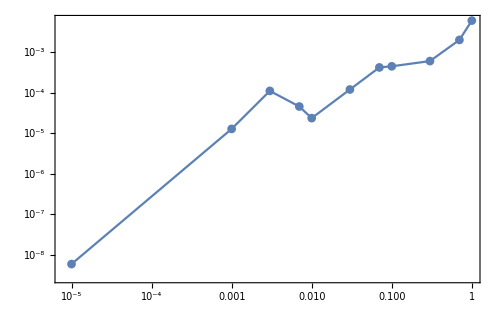

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@((δ50V-δVs1)/1)}],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->500]
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus5,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus5},{{c2,0,1},{d1,0,1}},MaxIterations->10000,AccuracyGoal->12,WorkingPrecision->50,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: 微分方程的精度 ({{200 (1.×10^-10+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678861791139950348750940229934936418635795250784) 小于 WorkingPrecision (50.).

End with 1.4484139s

NDSolve::precw: 微分方程的精度 ({{200 (0.00001+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.213611308320801299029844291034704416808056085508) 小于 WorkingPrecision (50.).

End with 1.0312561s

NDSolve::precw: 微分方程的精度 ({{200 (1.×10^-10+0.398942 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00067881310436079970372691180621077543994706791807) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

End with 1.1875099s

End with 1.0781318s

End with 2.4062693s

End with 1.6875154s

End with 2.2968949s

End with 1.7438550s

End with 1.5156342s

End with 1.1718849s

End with 1.3750070s

End with 1.2656347s

{1.0001845949278224643206860450719286593781921460291,1.2701959541702836010024887896291884748887057520195,4.6550115×10^-12,1.6839498×10^-9}

End with 1.4843892s

End with 1.2031320s

End with 1.3281342s

End with 2.0937658s

End with 2.6206260s

End with 1.1250071s

End with 1.2031345s

End with 0.9375124s

End with 1.1406329s

End with 0.9531321s

{1.0003937398586001517483117743034716966628307782348,1.2264170766883137928848303475716868230409499903526,-1.642828×10^-12,-5.9376061×10^-10}

End with 1.2187614s

End with 1.0312582s

End with 2.3281424s

End with 1.7343862s

End with 2.3019627s

End with 1.7449512s

{1.0020441110086698664605175180543618234839518870223,1.0176014405934133470244387362169973871125400886056,1.0406885×10^-12,3.7637301×10^-10}

End with 2.4591566s

End with 1.7656251s

End with 1.2656273s

End with 1.4062628s

End with 1.2656323s

End with 1.4687634s

{1.0020440796866244984235356373001129603944881112472,1.0148906626904344754869836511364766433098934574781,2.9916583×10^-14,1.081943×10^-11}

End with 1.2500077s

End with 1.5156362s

End with 1.1875116s

End with 1.6149395s

End with 1.1875119s

End with 1.5468837s

{1.0020434875834399971453539952839557468500228334839,1.0148878110534156721401285900761507481470748288845,-2.0241263×10^-16,-7.320315×10^-14}

End with 1.1562600s

End with 1.5781477s

End with 2.3906295s

End with 1.4375131s

End with 2.3750189s

End with 1.3906365s

{1.0020434917299359388338542040126585524511864221257,1.014887808164281462786141076255098766616497019787,8.2303651×10^-22,2.9908879×10^-19}

End with 2.4176628s

End with 1.4531347s

End with 3.0996211s

End with 1.5312595s

End with 2.5937718s

End with 1.8386525s

{1.0020434917363248210371391678580575417068471816583,1.0148878073198453239202588267825074942644420099303,-7.0466395×10^-24,-6.2126561×10^-22}

End with 2.8836185s

End with 1.5786978s

End with 1.5415310s

End with 1.3829758s

End with 1.5758625s

End with 1.5611822s

{1.0020434917112366955040665108349379394898297810432,1.0148878106270749692312861494749825264362515509864,-2.3035989×10^-23,-3.1415998×10^-21}

End with 3.5434544s

End with 1.8583103s

End with 1.7102059s

End with 1.7332215s

End with 1.7482331s

End with 1.8122791s

{1.0020434917511750505010484077320498780444140195011,1.0148878053622147766965838718851572624814941377837,1.2367433×10^-23,1.2650887×10^-21}

End with 2.7799618s

End with 1.9713899s

End with 2.0645485s

End with 1.4800439s

End with 2.0792013s

End with 1.1818320s

{1.0020434917408715168674686626956021076893597338039,1.0148878067204767228283645810508497520231807564076,6.4919375×10^-24,2.934025×10^-21}

End with 2.8234948s

End with 1.5200706s

End with 2.7229205s

End with 1.1668242s

End with 2.7789592s

End with 1.1488102s

{1.0020434917418794197011441730881571449002753101681,1.0148878065876107313062256996185839076268538008195,-3.2079363×10^-25,1.4646844×10^-21}

End with 2.6968992s

End with 1.5010610s

End with 1.4697151s

End with 1.8623136s

End with 1.4550241s

End with 1.7722521s

{1.0020434917416967978405607211505760178331090724699,1.0148878066116848252413432391245512163733233252081,2.1413922×10^-24,-8.9967998×10^-22}

End with 2.6818934s

End with 1.4910540s

End with 1.5320819s

End with 1.0897684s

End with 1.5661038s

End with 1.0737595s

{1.002043491741625266275445054454240595954626577342,1.0148878066211144700750743439284169122134157004569,2.5381254×10^-24,2.8405447×10^-22}

End with 1.5470881s

End with 1.0667659s

End with 1.7472317s

End with 1.3209328s

End with 1.7962674s

End with 1.3439460s

{1.0020434917402329125302948445727422448048305212954,1.0148878068046614132637160431368756159994468040064,4.33406×10^-25,9.7887327×10^-22}

End with 1.5050626s

End with 1.1488086s

End with 1.5701043s

End with 1.8192859s

End with 1.5570973s

End with 1.8588128s

{1.002043491740232993014988180698003412949010846913,1.0148878068046508034085334661987695330096898064873,5.9901948×10^-25,-1.2757304×10^-21}

End with 1.5292286s

End with 1.1374964s

End with 1.7560897s

End with 1.3011769s

End with 1.7753415s

End with 1.4184904s

{1.0020434917402113646038982735041390512620519300869,1.0148878068075019673127694960995841342245148002714,9.8105127×10^-24,4.8223595×10^-21}

End with 1.4980558s

End with 1.1097849s

End with 2.6478670s

End with 1.1337974s

End with 2.6348723s

End with 1.0787484s

{1.0020434917402842117887625475221762293037074207661,1.0148878067978988918366079698061522620273586807856,3.3612934×10^-24,2.5234408×10^-21}

End with 1.4930521s

End with 1.1047792s

End with 1.5380865s

End with 1.5791230s

End with 1.4470176s

End with 1.5020608s

{1.0020434917402584917765418775839440958481702491196,1.0148878068012894307992564162964079939991838811521,5.3003015×10^-24,1.23327×10^-21}

End with 1.5841153s

End with 1.1840806s

End with 1.4460220s

End with 1.3389451s

End with 1.4890513s

End with 1.3229326s

{1.0020434917404080162372086337629888932990548761624,1.0148878067815783783545723400200201638285784246739,1.8156004×10^-24,1.1722249×10^-21}

End with 1.4562352s

End with 1.1718853s

End with 1.7031375s

End with 1.2812633s

End with 1.5156363s

End with 1.2656327s

{1.002043491740259554173178738438788302139706017901,1.0148878068011493804306890081994300882011647207886,8.322096×10^-24,3.2582079×10^-21}

End with 1.4531512s

End with 1.0937437s

End with 1.7031400s

End with 1.1406329s

End with 1.7646152s

End with 1.1718820s

{1.0020434917403049818114975529888914367285805715419,1.014887806795160884920673947228267768882930984764,5.9890489×10^-24,1.8637247×10^-21}

End with 1.4687577s

End with 1.0312557s

End with 1.4788973s

End with 1.0937453s

End with 1.4218828s

End with 1.1093842s

{1.0020434917403357960292575768382478827700234352571,1.0148878067910988026392778016660003492998682270916,1.9893402×10^-24,2.8331868×10^-22}

End with 1.5625132s

End with 1.0221957s

End with 1.4062665s

End with 1.2656376s

End with 1.4967864s

End with 1.4062610s

{1.0020434917410768085389988430878889592459265778874,1.0148878066934148760325828327452362783751042516022,-1.2850979×10^-25,-9.3803275×10^-23}

End with 1.4687622s

End with 1.2968826s

End with 1.8750159s

End with 1.2187553s

End with 1.9687653s

End with 1.2343881s

{1.0020434917399485222996985685537896903348125271059,1.0148878068421511372188278327462429012787671104884,2.4921801×10^-24,7.2569124×10^-22}

End with 1.4062587s

End with 1.3125116s

End with 1.4403545s

End with 1.0625032s

End with 1.4531397s

End with 1.0156290s

{1.0020434917409893656973540452699500887392434536492,1.0148878067049420230283788178895236314065352525467,2.4677783×10^-24,3.5083122×10^-22}

End with 1.4218803s

End with 1.2968855s

End with 1.7031413s

End with 1.4531343s

End with 1.8125287s

End with 1.4915631s

{1.0020434917377390826416225923691172409917696099035,1.0148878071334103785463102534214625392865898224071,-3.3524751×10^-24,-8.6536084×10^-22}

End with 1.4687622s

End with 1.2187626s

End with 2.0312648s

End with 1.2187598s

End with 1.9531522s

End with 1.2187499s

{1.0020434917426356720346003311426103122416054162876,1.0148878064879177956292293793149827246397067546218,4.5704343×10^-24,2.2404283×10^-21}

End with 1.4531326s

End with 1.2343844s

End with 1.9375137s

End with 1.0000086s

End with 1.8521558s

End with 1.0155712s

{1.0020434917411835333557047528720084515032213828527,1.0148878066793458839100973600442533354119408659634,6.3163404×10^-24,2.2449266×10^-21}

End with 1.3750074s

End with 1.2343860s

End with 1.5840299s

End with 1.3437608s

End with 1.6406373s

End with 1.3593866s

{1.0020434917411724629683293406711157276029714920592,1.014887806680805237016383017594698881295790853621,3.9968039×10^-24,-2.3395648×10^-22}

End with 1.4062614s

End with 1.3281317s

End with 1.6406393s

End with 1.4754250s

End with 1.6562626s

End with 1.4218865s

{1.0020434917409070651142676410727460770600207559328,1.0148878067157912921192711983489012890632446644367,2.6894576×10^-24,2.5736932×10^-21}

End with 1.4375126s

End with 1.3437583s

End with 1.7656419s

End with 1.5468882s

End with 1.7031384s

End with 1.5000133s

{1.002043491741071436497381619255636918247365199075,1.0148878066941230450744904126985737518091913098525,1.8389352×10^-24,3.3769882×10^-22}

{1.002043491741071436497381619255636918247365199075,1.0148878066941230450744904126985737518091913098525}

```mathematica
Module[{shift=10,d=2000,n=20,ev},{ev,efVs2}=NDEigensystem[{shift f[r]+Vs2[r,a,{c2,d1}] f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f,{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShiftedVs2=ev-shift]
```

$Aborted

```mathematica
ParallelTable[Module[{eeee,timea,timeb},
Print[n];
timea=SessionTime[];
eeee=EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{1.*10^-19,3000},{0.99 SetPrecision[#[[n]],3],1.01 SetPrecision[#[[n]],3]}&[Table20REE],{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-2},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}];
timeb=SessionTime[];
Print[eeee,"    end with ",timeb-timea,"s"];
energyVs2[[n]]=eeee],{n,20,1,-1}]
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{u0,5000.}]
```

EigenEnergy[-0.399758 ⅇ^(-5000. r^2)+1.59418×10^-10 (-1.90481×10^9 ⅇ^(-5000. r^2)+6.34936×10^12 ⅇ^(-5000. r^2) r^2)-(0.01 Erf[70.7107 r])/r,200,{1/100000000000000000000,5000.}]

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
```

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.003+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.01+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (0.07+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.213592724017438889916201725500577859161388367374) is less than WorkingPrecision (50.).

End with 2.0816038s

{1/100000,-0.21043067293094009709750199431015234489308642556029}    2.081604

NDSolve::precw: The precision of the differential equation ({{200 (0.001+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.778437) is less than WorkingPrecision (50.).

End with 5.1753795s

{0.003,-0.66145360267389184375147288235398984705259528662533}    5.191003

NDSolve::precw: The precision of the differential equation ({{200 (0.007+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==1.06888) is less than WorkingPrecision (50.).

End with 3.4062775s

{0.001,0.81867970935025715627669845398741447522068974839229}    3.421903

NDSolve::precw: The precision of the differential equation ({{200 (0.1+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.28426) is less than WorkingPrecision (50.).

End with 11.8785556s

{0.01,-0.90920313441278911018369727050225811480714740515822}    11.894181

NDSolve::precw: The precision of the differential equation ({{200 (0.03+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.478119) is less than WorkingPrecision (50.).

End with 7.9531871s

{0.007,0.4459897912044233958740299505897011717962438579552}    7.9688133

NDSolve::precw: The precision of the differential equation ({{200 (0.3+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.17589) is less than WorkingPrecision (50.).

End with 32.9880777s

{0.07,0.17410884315278871498728131152222867407958496031609}    33.066212

NDSolve::precw: The precision of the differential equation ({{200 (0.7+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.23368) is less than WorkingPrecision (50.).

End with 22.4064076s

{0.03,0.22956086971356967875693824755724158759909023333806}    22.453282

NDSolve::precw: The precision of the differential equation ({{200 (1+0.399758 Power[«2»]-1.59418×10^-10 Plus[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.630566) is less than WorkingPrecision (50.).

End with 37.2569303s

{0.1,-0.56259207152597519370509096000410839673828300444393}    37.31943

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.25818) is less than WorkingPrecision (50.).

End with 56.5475328s

{0.3,-1.4123448646205405044171387718269287862834659733541}    56.672529

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.506588) is less than WorkingPrecision (50.).

End with 78.0253976s

{0.7,-0.46890380198106618965717320117901739073220858410473}    78.1660289

FindRoot::precw: The precision of the argument function (Tan[δ]==-12.76631442508893972696858629325751734328649807) is less than WorkingPrecision (50.).

End with 91.1420132s

{1,-1.492624803873530705029428581390362516549150312697}    91.2982649

{-0.21043067293094009709750199431015234489308642556029,0.81867970935025715627669845398741447522068974839229,-0.66145360267389184375147288235398984705259528662533,0.4459897912044233958740299505897011717962438579552,-0.90920313441278911018369727050225811480714740515822,0.22956086971356967875693824755724158759909023333806,0.17410884315278871498728131152222867407958496031609,-0.56259207152597519370509096000410839673828300444393,-1.4123448646205405044171387718269287862834659733541,-0.46890380198106618965717320117901739073220858410473,-1.492624803873530705029428581390362516549150312697}

## Matrix element <p^4>

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_energyVs1_2nd.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_c1_2nd.mx"]
```

Get::noopen: 无法打开 C:\Users\ASUS\Documents\DataDump_Coulomb_7_energyVs1_2nd.mx.

$Failed

Get::noopen: 无法打开 C:\Users\ASUS\Documents\DataDump_Coulomb_7_c1_2nd.mx.

$Failed

```mathematica
<<C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1_3rd.mx
```

Get::noopen: 无法打开 C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1_3rd.mx.

$Failed

```mathematica
nRange=20;
```

```mathematica
p4Ture[n_,b_][Z_,γ_,opt___]:=Z NIntegrate[(Laplacian[efVs1[[n]],{r}]^2),{r,0,If[n>15,4000,b]},opt]+γ/a NIntegrate[efVs1[[n]]^2 δa[r],{r,0,If[n>15,4000,b]},opt](*+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]*)
```

```mathematica
REAL=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange}];
REF=Table[Integrate[D[r RS[n,r],{r,2}]^2,{r,0,∞}],{n,nRange-2,nRange}];
```

### Matrix element in V_eff^(a^2)

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504158273109948804989145348 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

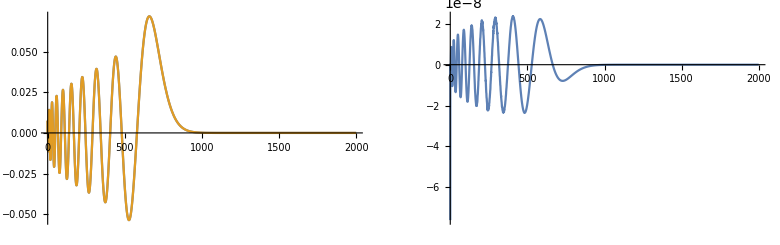
{316.214,-Graphics-}

```mathematica
AbsoluteTiming@Module[{n=19},ef=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef];
GraphicsGrid@{{Plot[{ef,r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium],
Plot[{ef-r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium]}}
]
```

```mathematica
NIntegrate[(D[ef,{r,2}])^2,{r,1.*10^-50,4000},Exclusions->50]
Abs@((%-REAL[[20]])/REAL[[20]])
```

0.00103203

0.0517522

```mathematica
AbsoluteTiming[efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0500078698243863935055737602971 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00312500761726746385913647922606 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00102040862718159308244150419666 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00050000007796292676973750649047 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000413223188903938793994512264818 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000781250237936304904722289140259 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00200000249550536888652531039438 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000347222253552894523182159148667 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000617284082651037569419393087846 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00138888989166308326560993291706 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000295858009162576239009167422901 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000222222232488422260934584517289 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000173010386113415734680628773593 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000255102055311667723228331312929 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0125002441801421361773951351802 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000195312507434709104520394621199 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504158273109948804989145348 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00555558766918009791462567717346 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000154320991780025227507069598258 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000125000002436179368929957388996 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{2445.63,{8.41457014008×10^-818                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-5.480197172726×10^-380                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],8.39339×10^-233                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.14087×10^-158                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],3.44212×10^-113                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.2177×10^-82                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.63894×10^-60                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.11706×10^-43                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.11448×10^-30                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.23154×10^-19                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.02554×10^-10                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.00340555                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],9183.21                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-3.3482×10^9                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.39999×10^14                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.12086×10^-31                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],4.58687×10^-24                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-1.70214×10^-17                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],1.40823×10^-11                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-3.21204×10^-6                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
Module[{n=14,efunction},
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]];
efVs1[[n]]=efunction[[n]]
]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1_3rd.mx",efVs1];
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,If[#>15,4000,2000]},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (7.08049906424×10^-1635 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{45,44},{46,45},{47,46},{48,47},{49,48},{50,49},«33464»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4623668815636586952048333778507701378928326188347611607266528355568406087082334849813321133116737352}. NIntegrate obtained 4.24775143448205958754880454950146237906635095041566811870478274004760680511885743899799314631144069 and 9.4294993357277365201116231630111112705893449190092986268406862750987694486421162445050224791268157×10^-20 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (3.0032561052×10^-759 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4659802004911373337071412325364140666142675879536833723647658789795401373362383226469339285990687524}. NIntegrate obtained 0.7174212809199777929012894664292984532181745825076807971498109279693081909549759755618068069181562719 and 3.633547634066690580084017448059494709124396188637866489408592955265507683293373880163695855550865649×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (7.04490049372286×10^-465 («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4876851693547784171767109075724296318712432966469218138641756757990863061327905245533927872319965803}. NIntegrate obtained 0.2310293704005218476208680659105967534842423940550152647074475234522278493705018614045060625254064782 and 1.565100318490618058414719654037227888225773080342227279351087081435626816539107499249587825522316916×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.01984903187431712853938055156973597616852240651017562336163919592199692943063748185718615390076255168 and 2.074762998997241455182522314947624539621804802400464589855355901814498606670080863891670931669490639×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0134018318956914725368765651229453202777814174071243471793431669035110112443153993803885775000156491 and 1.349272075646587028220132847748484682868033567759296291558026803594026509245122889347926101283489337×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.009469642671235533884112092422123566763653524626848019889082198752430783453376630716086874204278076897 and 9.499293015886584565705581065264491615077331817953452020612324005259862951024457468747029254543415047×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{4.24775,0.717421,0.231029,0.101363,0.053096,0.0311892,0.019849,0.0134018,0.00946964,0.00693668,0.00523211,0.0040432,0.00318883,0.00255916,0.00208492,0.00172097,0.00143703,0.00121227,0.00103203,0.000885825}

{0.15045,0.11702,0.108887,0.105207,0.103108,0.101751,0.100801,0.1001,0.0995605,0.0991327,0.0987853,0.0984974,0.098255,0.098048,0.0978694,0.0977135,0.0975763,0.0974547,0.0973461,0.0972486}

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,If[#>15,4000,2000]][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{(*15,*)20})==(REF[[#]]&/@{(*2,*)3})](*/.Z->1*),{γ,-1,-10},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10,MaxIterations->10000]
((p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{15,20})-(REF[[#]]&/@{2,3}))/(REF[[#]]&/@{2,3})/.RESVs1
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.000885825 and 1.79075×10^-9 for the integral and error estimates.

FindRoot::precw: The precision of the argument function ({0.000885825+0.000282618 γ==157/160000}) is less than WorkingPrecision (50.).

{γ→0.33764725954412159015702246610372791534324179410807}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.000885825 and 1.79075×10^-9 for the integral and error estimates.

{1.02139,9.66804×10^-17}

```mathematica
p4Vs1=p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (7.08049906424×10^-1635 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},«37»,{45,44},{46,45},{47,46},{48,47},{49,48},{50,49},«33464»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (3.0032561052×10^-759 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.558842}. NIntegrate obtained 0.00838342 and 0.0000125049 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.00172097 and 3.23177×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.551043}. NIntegrate obtained 0.00143703 and 2.82697×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{5.01942,0.813096,0.259336,0.113299,0.0592056,0.0347244,0.0220751,0.0148931,0.0105169,0.00770014,0.00580569,0.004485,0.00353632,0.00283738,0.00231112,0.00190735,0.00159242,0.00134317,0.00114333,0.00098125}

{0.00388414,0.000734028,0.000295047,0.000156002,0.0000949686,0.0000629033,0.0000440104,0.0000319552,0.0000237978,0.0000180236,0.0000137876,0.0000105888,8.11453×10^-6,6.20316×10^-6,4.50098×10^-6,3.31483×10^-6,2.25921×10^-6,1.37747×10^-6,6.32936×10^-7,0.}

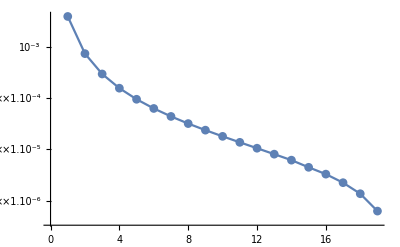

```mathematica
ListLogPlot[%161,Joined->True,PlotMarkers->{Automatic}]
```

### Matrix element in V_eff^(a^4)

```mathematica
efVs2=Module[{ef,am},
ef=Eigenfun[Vs2[r,a,c1],energyVs2];
am=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
(am[[2#]]=-am[[2#]])&@Range@10;
Table[am[[n]]f[r]/.ef[[n]],{n,20}]
]
```

```mathematica
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[{(RS[n,r]r),efVs1[r]},{r,0,2000},PlotRange->Full,ImageSize->Medium,PlotStyle->{Blue,Orange}],{n,20}],4]
AbsoluteTiming@GraphicsGrid@Partition[Table[Plot[(RS[n,r]r)-efVs1[r],{r,0,2000},PlotRange->Full,ImageSize->Medium],{n,20}],4]
```

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange
N[%,6]
Abs@((REAL-FALSE)/REAL);
N[%,6]
```

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{10,15,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->6,PrecisionGoal->6]
```

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```

## ψ_0 in effective theory

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
REALψ0=Limit[RS[#,r]/(√(4π)),r->0]&/@Range@nRange;
REF=Limit[RS[#,r]/(√(4π)),r->0]&/@{15,20};
```

```mathematica
FALSEψ0=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],Table20REE[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction=If[OddQ[n],efunction,-efunction];
NLimit[efunction[[n]]/(√(4π)r),r->0]&/@Range@nRange,{n,1,20}]
]
N[%,6]
Abs@((REALψ0-FALSEψ0)/REALψ0);
N[%,6]
```

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.003125 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.00102041 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.05 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.0005 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

$Aborted

$Aborted

{1.77245 Abs[0.56419-1. FALSEψ0],5.01326 Abs[0.199471-1. FALSEψ0],9.20994 Abs[0.108578-1. FALSEψ0],14.1796 Abs[0.0705237-1. FALSEψ0],19.8166 Abs[0.0504627-1. FALSEψ0],26.0496 Abs[0.0383882-1. FALSEψ0],32.8263 Abs[0.0304634-1. FALSEψ0],40.1061 Abs[0.0249339-1. FALSEψ0],47.8563 Abs[0.0208959-1. FALSEψ0],56.0499 Abs[0.0178412-1. FALSEψ0],64.6642 Abs[0.0154645-1. FALSEψ0],73.6795 Abs[0.0135723-1. FALSEψ0],83.0788 Abs[0.0120368-1. FALSEψ0],92.8468 Abs[0.0107704-1. FALSEψ0],102.97 Abs[0.00971154-1. FALSEψ0],113.437 Abs[0.00881546-1. FALSEψ0],124.236 Abs[0.00804918-1. FALSEψ0],135.358 Abs[0.00738782-1. FALSEψ0],146.793 Abs[0.00681231-1. FALSEψ0],158.533 Abs[0.00630783-1. FALSEψ0]}

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000173010386113415734680628773593 f[r],f[5000]==1.×10^-50,f'[5000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

$Aborted

```mathematica
AbsoluteTiming[Module[{efunction=Range@20},
SetSharedVariable[efunction,efVs1];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>18,8000,6000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]];
efVs1[[n]]=efunction[[n]],{n,16,20}]
]]
```

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000195312507434709104520394621199 f[r],f[6000]==1.×10^-50,f'[6000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000154320991780025227507069598258 f[r],f[6000]==1.×10^-50,f'[6000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000138504158273109948804989145348 f[r],f[8000]==1.×10^-50,f'[8000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000125000002436179368929957388996 f[r],f[8000]==1.×10^-50,f'[8000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000173010386113415734680628773593 f[r],f[6000]==1.×10^-50,f'[6000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{3760.89,{-6.67489×10^-83                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 6000.0000000000000000000000000000000000000000000000}}, <>][r],3.57496×10^-72                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 6000.0000000000000000000000000000000000000000000000}}, <>][r],-1.45604×10^-62                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 6000.0000000000000000000000000000000000000000000000}}, <>][r],2.83748×10^-97                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 8000.0000000000000000000000000000000000000000000000}}, <>][r],-5.37628×10^-87                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 8000.0000000000000000000000000000000000000000000000}}, <>][r]}}

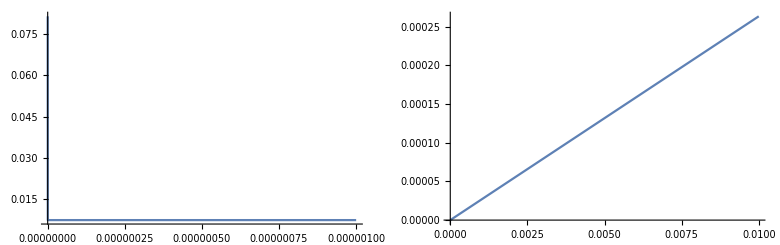

```mathematica
GraphicsGrid@{{Plot[efVs1[[17]]/(√(4π)r),{r,0,0.000001},ImageSize->Medium,PlotRange->Full],Plot[efVs1[[17]],{r,0,0.01},ImageSize->Medium]}}
```

```mathematica
Module[{ef,n=17},
ef=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{10000,1.*10^-10},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef];
{GraphicsGrid@{{Plot[efVs1[[n]]/(√(4π)r),{r,0,0.000001},ImageSize->Medium,PlotRange->Full],Plot[efVs1[[n]],{r,0,0.01},ImageSize->Medium]}},NLimit[ef/(√(4π)r),r->0],Abs@((REALψ0[[n]]-NLimit[ef/(√(4π)r),r->0])/REALψ0[[n]])}
]
```

NDSolve::precw: The precision of the differential equation ({{(-0.439393 Power[«2»]-0.1 Power[«2»] Erf[«1»]) f[r]-f''[r]/20==-0.000173010386113415734680628773593 f[r],f[10000]==1.×10^-100,f'[10000]==-1.×10^-100},{},{},{},{}}) is less than WorkingPrecision (50.).

$Aborted

```mathematica
NLimit[efVs1[[19]]/(√(4π)r),r->0,WorkingPrecision->50,Scale->10]
Abs@((REALψ0[[13]]-%)/REALψ0[[13]])
```

0.0111071

0.0772321

```mathematica
FALSEψ0[[13]]=%%
```

0.0111071

```mathematica
FALSEψ0
Abs@((REALψ0-FALSEψ0)/REALψ0)
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit::noise will be suppressed during this calculation.

{0.520927,0.184088,0.100197,0.0650787,0.0465654,0.0354238,0.0281106,0.0230083,0.0192821,0.0164633,0.0142701,0.0125241,0.0111071,0.0099386,0.00896149,0.00813462,NLimit[1/r 1.29393×10^-24                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],r→0],0.00680714,NLimit[1/r 3.97254×10^-12                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],r→0],NLimit[-1/r 9.061×10^-7                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],r→0]}

{0.0766804,0.0771208,0.077189,0.0772086,0.0772301,0.0772235,0.0772316,0.0772284,0.0772296,0.0772314,0.0772383,0.0772317,0.0772321,0.0772324,0.0772327,0.0772329,17 √(17 π) Abs[1/(17 √(17 π))-NLimit[1/r 1.29393×10^-24                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],r→0]],0.0785994,19 √(19 π) Abs[1/(19 √(19 π))-NLimit[1/r 3.97254×10^-12                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],r→0]],40 √(5 π) Abs[1/(40 √(5 π))-NLimit[-1/r 9.061×10^-7                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],r→0]]}

```mathematica
FALSEψ0=Table[
NLimit[efVs1[[n]]/(√(4π)r),r->0,WorkingPrecision->50,Scale->10],{n,1,20}];
N[%,6]
Abs@((REALψ0-FALSEψ0)/REALψ0);
N[%,6]
```

{0.5209,0.18409,0.100197,0.0650786,0.046566,0.0354238,0.0281108,0.0230083,0.0192821,0.0164634,0.0142702,0.0125241,0.0111071,0.0099386,0.00896149,0.00813462,0.00742752,0.00681723,0.00628617,0.00582066}

{0.0767,0.07712,0.0771874,0.0772089,0.0772185,0.0772235,0.0772265,0.0772284,0.0772296,0.0772306,0.0772312,0.0772317,0.0772321,0.0772324,0.0772327,0.0772329,0.077233,0.0772332,0.0772348,0.0772334}

```mathematica
ψ0True[n_,d_][γ_,{optpsi___}]:=√(4π)(γ NIntegrate[efVs1[[n]]/r δa[r] r^2,{r,0,d},optpsi](*+η a^2 NIntegrate[efVs2[[n]][r]Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,d},opt]*))
```

```mathematica
Thread[ψ0True[#,8000][γ,{MaxRecursion->20}]&/@{20}==(REF[[#]]&/@{2})]
```

{0.00530633 γ==1/(40 √(5 π))}

```mathematica
RES=FindRoot[Thread[ψ0True[#,8000][γ,{MaxRecursion->20}]&/@{20}==(REF[[#]]&/@{2})],{γ,0,-2},AccuracyGoal->10,MaxIterations->100000,WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ({0.00530633 γ==1/(40 √(5 π))}) is less than WorkingPrecision (30.).

{γ→1.18873762444377185616966305914}

```mathematica
ψ0Vs1=ψ0True[#,If[#>15,4000,2000]][γ,{MaxRecursion->20}]&/@Range@nRange/.RES;
N[%,6]
Abs@((REALψ0-ψ0Vs1)/REALψ0);
N[%,6]
```

{0.567373,0.199744,0.108643,0.0705469,0.050473,0.0383935,0.0304664,0.0249357,0.020897,0.017842,0.015465,0.0135726,0.012037,0.0107706,0.00971164,0.00881553,0.00804922,0.00738784,0.00681232,0.00630783}

{0.00564333,0.00137038,0.000597444,0.00032901,0.000205254,0.000138191,0.0000978207,0.0000716493,0.0000537224,0.0000409083,0.0000314326,0.0000242289,0.0000186249,0.0000141798,0.0000105947,7.66147×10^-6,5.23089×10^-6,3.19436×10^-6,1.47075×10^-6,3.17597×10^-12}

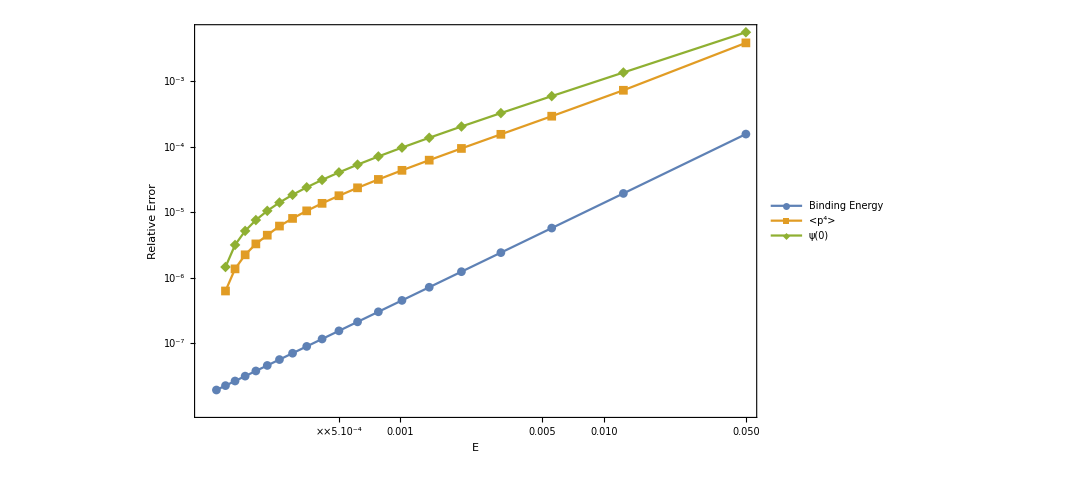

```mathematica
ListLogLogPlot[Transpose[{Take[-Table20REE,20]}~Join~{#}]&/@{{0.00015739648772772338,0.000019534411370702994,5.780452417506603*^-6,2.437525588178113*^-6,1.2477526841608853*^-6,7.219974198190148*^-7,4.5463796115828564*^-7,3.0455847011001675*^-7,2.138946806782768*^-7,1.5592585339216367*^-7,1.1714753157874948*^-7,9.023233597804657*^-8,7.096950740731639*^-8,5.682173742378032*^-8,4.6197899997678364*^-8,3.806571044484563*^-8,3.173554266274781*^-8,2.6734563391209162*^-8,2.2731853470967297*^-8,1.948943480559184*^-8},{0.0038841356363130686,0.0007340281598998262,0.00029504742006645053,0.00015600170713539761,0.00009496861109357971,0.00006290328011691049,0.00004401043795760054,0.000031955178775573306,0.00002379781106303881,0.000018023550756683353,0.000013787590644461068,0.000010588837727095126,8.114525149303155*^-6,6.2031564812946524*^-6,4.5009819286642765*^-6,3.3148301280334638*^-6,2.2592098924950075*^-6,1.3774685937934493*^-6,6.329364347367914*^-7,0.},{0.005643332465597392,0.0013703845189107892,0.0005974438186516103,0.00032900986491460945,0.00020525436646088175,0.00013819145853864162,0.00009782065269368042,0.00007164932781051687,0.0000537223571384434,0.00004090825331537771,0.00003143260204712803,0.00002422892350663096,0.00001862494043098393,0.000014179801241243686,0.000010594710904844424,7.661467865335665*^-6,5.230887889826618*^-6,3.1943619211847617*^-6,1.4707481633691188*^-6,0}},Joined->True,PlotLegends->{"Binding Energy","<p^4>","ψ(0)"},ImageSize->800,Frame->True,PlotRange->Automatic,PlotMarkers->Automatic,FrameLabel->{"E","Relative Error"},RotateLabel->True]
```

```mathematica
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Test_Coulomb_7.eps",%]
```

C:\Users\ASUS\OneDrive\Documents\Test_6\Test_Coulomb_7.eps